# Gra w życie - raport końcowy

## Autorzy: Kacper Cholewiński, Bartosz Szymański, Maksymilian Tabian

## 1. Przedstawienie i omówienie wyników

## 1. Wykorzystane narzędzia

W poniższym kodzie skorzystano z wbudowanych funkcji dostępnych w języku Wolfram :

Funkcja CellularAutomation

Służy ona do symulowania automatów komórkowych. Automaty komórkowe to  modele obliczeniowe, w których przestrzeń jest podzielona na komórki, a stan każdej komórki zmienia się w zależności od stanu jej sąsiadów.

Funkcja ta pozwala na badanie fascynujących zachowań i wzorców, które mogą pojawić się w automatach komórkowych w zależności od wybranej reguły.

Funkcja gameOfLife = {224, {2, {{2, 2, 2}, {2, 1, 2}, {2, 2, 2}}}, {1, 1}};

224 to liczba całkowita, która reprezentuje regułę dla automatu komórkowego. W przypadku gry w życie używa się liczby całkowitej zapisanej w systemie dwójkowym. Liczba 224 w systemie dwójkowym to “11100000”. W kontekście gry w życie oznacza to regułę 224 z zestawu reguł, które decydują, czy komórka będzie żywa czy martwa w następnym pokoleniu w zależności od stanu swoich sąsiadów.

{2, {{2, 2, 2}, {2, 1, 2}, {2, 2, 2}}}  to struktura określająca, jakie sąsiedztwo jest brane pod uwagę przy ewolucji komórek. W grze w życie przyjmuje się zazwyczaj sąsiedztwo von Neumanna, a ta struktura odpowiada za to. Wzór {{2, 2, 2}, {2, 1, 2}, {2, 2, 2}} oznacza, że brane są pod uwagę wszystkie komórki w otoczeniu o promieniu 1 (łącznie z komórką środkową), a wartość 1 oznacza, że dana komórka jest brana pod uwagę przy ewolucji.

{1, 1}: Trzeci element to pozostałe parametry reguły. W tym przypadku {1, 1} oznacza, że nowa komórka stanie się żywa (1), jeśli ma dokładnie 3 żywych sąsiadów, a pozostanie żywa, jeśli ma 2 lub 3 żywych sąsiadów.

```mathematica
gameOfLife = {224,{2,{{2,2,2},{2,1,2},{2,2,2}}},{1,1}};
```

## 2. Struktury niezmienne

Struktury niezmienne (Still lifes) to układy komórek, które nie zmieniają się w kolejnych turach gry. Dlatego mogą zostać uznane za oscylatory z okresem 1 (Patrz: podrozdział 3)

Strict still lifes

Wśród układów komórek Still lifes wyróżniamy Strict still lifes, które są albo jedną wyspą, albo są układem kilku wysp, takim, że usunięcie przynajmniej jednej wyspy niszczy stabilność układu.
Wyspa to układ połączonych komórek (mających wspólną krawędź lub wierzchołek). Poniżej przedstawiono przykłady układów still lifes [1]

### Przykład 1. Beehive

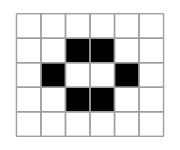

```mathematica
board1 = ConstantArray[0, {5,6}];
board1[[2,{3,4}]] = board1[[3, {2,5}]] = board1[[4, {3,4}]] = 1;
ArrayPlot[board1, Mesh->Automatic, ImageSize->Small]
```

Beehive należy do strict still lifes, ponieważ jest  układem połączonych komórek tworzących stabilną strukturę.

### Przykład 2. Beehive with tail

```mathematica
board2 = ConstantArray[0, {7,8}];
board2[[2,{3,4}]] = board2[[3, {2,5}]] = board2[[4, {3,4,6}]] =board2[[5,6]]= board2[[6, {6,7}]] =  1;
ArrayPlot[board2, Mesh->Automatic, ImageSize->Small]
```

-Graphics-

Beehive with tail  jest uznawany za strict still life, ponieważ jest układem połączonych komórek tworzących stabilną strukturę. 
Na klasyfikację tą nie ma wpływu fakt, że obiekt ten zawiera mniejszy obiekt będący strict life.

### Przykład 3. Mirrored table

```mathematica
board3 = ConstantArray[0, {6,7}];
board3[[{2,5},{2,3,5,6}]] = board3[[{3,4}, {3,5}]]  =  1;
ArrayPlot[board3, Mesh->Automatic, ImageSize->Small]
```

-Graphics-

Mirrored table jest układem dwóch wysp (każda z nich jest obiektem, który nazywamy table), ale uznajemy go za strict still life, ponieważ table osobno nie jest stabilne.

```mathematica
board32 = ConstantArray[0, {6,7}];
board32[[{2,5},{2,3}]] = board32[[{3,4}, 3]]  =  1;
Dynamic[ArrayPlot[board3 = Last[CellularAutomaton[gameOfLife, board3, {{0, 1}}]], Mesh->Automatic, ImageSize->Small]]
Dynamic[ArrayPlot[board32 = Last[CellularAutomaton[gameOfLife, board32, {{0, 1}}]], Mesh->Automatic, ImageSize->Small]]
```

### Liczba obiektów typu strict still lifes

Liczba obiektów typu strict still lifes składających się z n komórek została wyliczona do n = 34  i wynosi dla kolejnych n = 1, 2, 3, .. odpowiednio 0, 0, 0, 2, 1, 5, 4, 9, 10, 25, 46, ...
Do n = 7 liczbę obiektów ustalił sam John Conway. [2]

n = 4

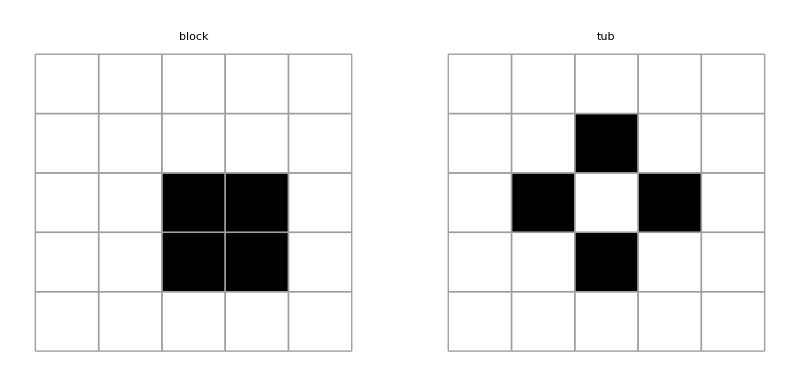

```mathematica
board41 = ConstantArray[0, {5,5}];
board42 = ConstantArray[0, {5,5}];
board41[[{3,4},{3,4}]] = 1;
board42[[{2,4}, 3]] =board42[[3,{2,4}]]= 1;
GraphicsRow[{ArrayPlot[board41, Mesh->Automatic,  ImageSize->Small, PlotLabel->"block"],
                            ArrayPlot[board42, Mesh->Automatic, ImageSize ->Small, PlotLabel->"tub"]}]
```

n = 5

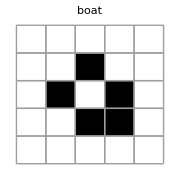

```mathematica
board5 = ConstantArray[0, {5,5}];
board5[[2,3]] =board5[[3,{2,4}]]= board5[[4, {3,4}]]=1;
ArrayPlot[board5, Mesh->Automatic, ImageSize->Small, PlotLabel->"boat"]
```

n = 6

```mathematica
board61 = ConstantArray[0, {6,6}];
board62 = ConstantArray[0, {6,6}];
board63 = ConstantArray[0, {6,6}];
board64 = ConstantArray[0, {6,6}];
board65 = ConstantArray[0, {6,6}];
board61[[4, {2,4,5}]]=board61[[5, {2,3,5}]] = 1;
board62[[3, {3,4}]] = board62[[4, {3,5}]] = board62[[5, {4,5}]] = 1;
board63[[3, {2,3}]] = board63[[4, {2,5}]] = board63[[5, {4,5}]] = 1;
board64[[{3,5}, {3,4}]] = board64[[4, {2,5}]] = 1;
board65[[2, 3]] = board65[[3, {2,4}]] = board65[[4, {3,5}]] = board65[[5, 4]] = 1;
```

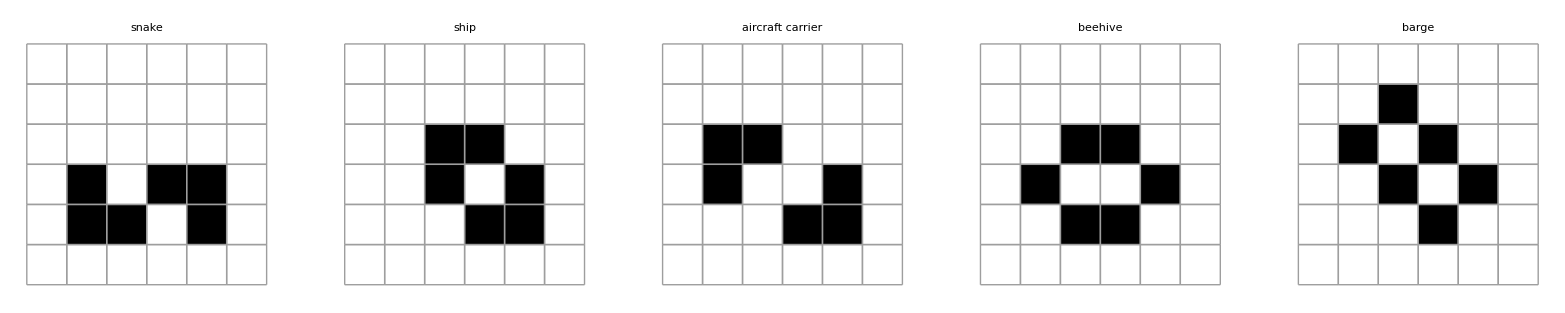

```mathematica
GraphicsRow[
{ArrayPlot[board61, Mesh->Automatic, PlotLabel->"snake"],
ArrayPlot[board62, Mesh->Automatic, PlotLabel->"ship"],
ArrayPlot[board63, Mesh->Automatic, PlotLabel->"aircraft carrier"],
ArrayPlot[board64, Mesh->Automatic, PlotLabel->"beehive"],
ArrayPlot[board65, Mesh->Automatic, PlotLabel->"barge"]}
]
```

n = 7

```mathematica
board71 = ConstantArray[0, {6,7}];
board72 = ConstantArray[0, {6,7}];
board73 = ConstantArray[0, {6,7}];
board74 = ConstantArray[0, {6,7}];
board71[[3, {5,6}]] = board71[[4, {2,4,6}]] = board71[[5,{2,3}]] = 1;
board72[[2, 4]] = board72[[3, {3,5}]] = board72[[4, {4,6}]] = board72[[5, {5,6}]] = 1;
board73[[2, {3,4}]] = board73[[3, {3,5}]] = board73[[4, 5]] = board73[[5, {5,6}]] = 1;
board74[[2,4]] = board74[[3, {3,5}]] = board74[[4, {3,6}]] = board74[[5, {4,5}]] = 1;
```

```mathematica
GraphicsRow[
{ArrayPlot[board71, Mesh->Automatic, PlotLabel->"long snake"],
ArrayPlot[board72, Mesh->Automatic, PlotLabel->"long boat"],
ArrayPlot[board73, Mesh->Automatic, PlotLabel->"eater 1"],
ArrayPlot[board74, Mesh->Automatic, PlotLabel->"loaf"]}
]
```

-Graphics-

## 3. Oscylatory

Niektóre układy komórek, zmieniają się w określony sposób, co pewien czas powracając do początkowego stanu. Liczba ruchów potrzebna do powrotu do stanu początkowego to okres oscylatora. 
Poniżej przedstawiono parę przykładów oscylatorów [1]

### Przykład 1. Blinker (światła uliczne)

```mathematica
b1 = ConstantArray[0, {5,5}];
b1[[2,{3}]] = b1[[3, {3}]] = b1[[4, {3}]] = 1;
DynamicModule[{currentGeneration = b1},Dynamic[ArrayPlot[currentGeneration =Last[CellularAutomaton[gameOfLife,currentGeneration, {{0, 1}}]], Mesh->Automatic, ImageSize->Small]]]
```

### Przykład 2. Toad (żabka)

```mathematica
b2 = ConstantArray[0, {6,6}];
b2[[2,{3}]] = b2[[3, {3,4}]] = b2[[4, {3,4}]]=b2[[5, {4}]] = 1;
DynamicModule[{currentGeneration = b2},
Dynamic[ArrayPlot[currentGeneration =Last[CellularAutomaton[gameOfLife,currentGeneration, {{0, 1}}]], Mesh->Automatic, ImageSize->Small]]]
```

### Przykład 3. Beacon

```mathematica
b3 = ConstantArray[0, {6,6}];
b3[[2,{2,3}]] = b3[[3, {2}]] = b3[[4, {5}]]=b3[[5, {4,5}]] = 1;
DynamicModule[{currentGeneration = b3},Dynamic[ArrayPlot[currentGeneration =Last[CellularAutomaton[gameOfLife,currentGeneration, {{0, 1}}]], Mesh->Automatic, ImageSize->Small]]]
```

### Przykład 4. Pulsar

```mathematica
b4 = ConstantArray[0, {17,17}];
b4[[{3,8,10,15},{5,6,7,11,12,13}]] = b4[[{5,6,7,11,12,13},{3,8,10,15}]]= 1;
DynamicModule[{currentGeneration = b4},Dynamic[ArrayPlot[currentGeneration =Last[CellularAutomaton[gameOfLife,currentGeneration, {{0, 1}}]], Mesh->Automatic]]]
```

### Przykład 5.

```mathematica
b5 = ConstantArray[0, {11,18}];
b5[[{5,7},{7,12}]] = b5[[6,{5,6,8,9,10,11,13,14}]]= 1;
DynamicModule[{currentGeneration = b5},Dynamic[ArrayPlot[currentGeneration =Last[CellularAutomaton[gameOfLife,currentGeneration, {{0, 1}}]], Mesh->Automatic]]]
```

## 4. Statki

Statki to struktury, które zmieniają się podobnie jak oscylatory. Różni je to, że statki dodatkowo się przesuwają. [3]

### Przykład 1. Glider (szybowiec)

```mathematica
s1 = ConstantArray[0, {20,20}];
s1[[3,{1,2,3}]] = s1[[2,3]]= s1[[1,2]]= 1;
DynamicModule[{currentGeneration = s1},Dynamic[ArrayPlot[currentGeneration =Last[CellularAutomaton[gameOfLife,currentGeneration, {{0, 1}}]], Mesh->Automatic]]]
```

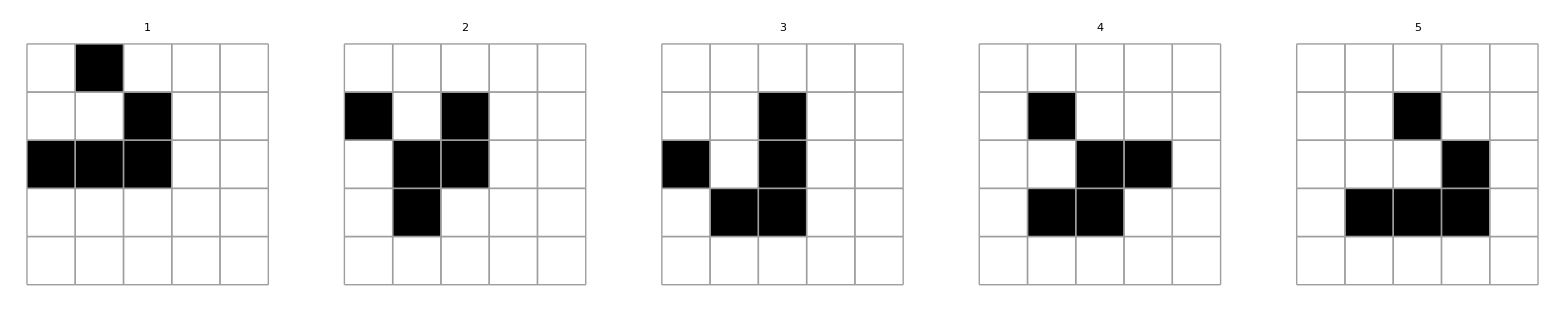

```mathematica
s11 = ConstantArray[0, {5,5}];
s11[[3,{1,2,3}]] = s11[[2,3]]= s11[[1,2]]= 1;
GraphicsRow[
{ArrayPlot[s11, Mesh->Automatic, PlotLabel->"1"],
ArrayPlot[s12 =Last[CellularAutomaton[gameOfLife,s11, {{0, 1}}]], Mesh->Automatic, PlotLabel->"2"],
ArrayPlot[s13 =Last[CellularAutomaton[gameOfLife,s12, {{0, 1}}]], Mesh->Automatic, PlotLabel->"3"],
ArrayPlot[s14 =Last[CellularAutomaton[gameOfLife,s13, {{0, 1}}]], Mesh->Automatic, PlotLabel->"4"],
ArrayPlot[s15 =Last[CellularAutomaton[gameOfLife,s14, {{0, 1}}]], Mesh->Automatic, PlotLabel->"5"],}
]
```

Przedstawiono cztery postacie szybowca, po czterech turach (okresie) struktura przesunęła się w dół i w lewo.

### Przykład 2. Light-weight spaceship (LWSS)

```mathematica
s2 = ConstantArray[0, {7,30}];
s2[[3,{3,4,5,6}]] = s2[[4,{2,6}]]= s2[[5,6]]=s2[[6,{2,5}]]= 1;
DynamicModule[{currentGeneration = s2},Dynamic[ArrayPlot[currentGeneration =Last[CellularAutomaton[gameOfLife,currentGeneration, {{0, 1}}]], Mesh->Automatic]]]
```

```mathematica
s21 = ConstantArray[0, {7,9}];
s21[[3,{3,4,5,6}]] = s21[[4,{2,6}]]= s21[[5,6]]=s21[[6,{2,5}]]= 1;
GraphicsRow[
{ArrayPlot[s21, Mesh->Automatic, PlotLabel->"1"],
ArrayPlot[s22 =Last[CellularAutomaton[gameOfLife,s21, {{0, 1}}]], Mesh->Automatic, PlotLabel->"2"],
ArrayPlot[s23 =Last[CellularAutomaton[gameOfLife,s22, {{0, 1}}]], Mesh->Automatic, PlotLabel->"3"],
ArrayPlot[s24 =Last[CellularAutomaton[gameOfLife,s23, {{0, 1}}]], Mesh->Automatic, PlotLabel->"4"],
ArrayPlot[s25 =Last[CellularAutomaton[gameOfLife,s24, {{0, 1}}]], Mesh->Automatic, PlotLabel->"5"],}
]
```

-Graphics-

Struktura ta przesuwa się w jednym kierunku o 2 jednostki w jednym okresie.

## 5. Struktury niestałe

Struktury niestałe ulegają zmianom i nigdy nie powracają do swojego początkowego stanu. Są to grupy struktur, trudne do zakwalifikowania do innych kategorii, co sprawia, że można wskazać wiele takich przykładów, często nawet poprzez losowe rozmieszczenie komórek na planszy początkowej.

### Przykład 1. Diehard

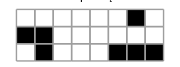

```mathematica
board1c = ConstantArray[0, {3,8}];
board1c[[1,{7}]] = board1c[[2, {1,2}]] = board1c[[3, {2,6,7,8}]]= 1;
ArrayPlot[board1c, Mesh->Automatic, ImageSize->Small,PlotLabel->"Plansza początkowa"]
DynamicModule[{currentGeneration = board1c},Dynamic[ArrayPlot[currentGeneration =Last[CellularAutomaton[gameOfLife,currentGeneration, {{0, 1}}]], Mesh->Automatic, ImageSize->Small]]]
```

Termin diehard (ang. die-hard - niereformowalny) oznacza układ, który znika po długim czasie. Powyżej przykład diehardu znikającego po 130 krokach. [1]

### Przykład 2. Najmniejszy nieśmiertelny układ

```mathematica
board3c = ConstantArray[0, {20,20}];
board3cp = ConstantArray[0, {6,8}];
board3c[[6,{7}]] = board3c[[7, {5,7,8}]] = board3c[[8, {5,7}]]= board3c[[9, {5}]]= board3c[[10, {3}]]= board3c[[11, {3,1}]]= 1;
board3cp[[1,{7}]] = board3cp[[2, {5,7,8}]] = board3cp[[3, {5,7}]]= board3cp[[4, {5}]]= board3cp[[5, {3}]]= board3cp[[6, {3,1}]]= 1;
ArrayPlot[board3cp, Mesh->Automatic, ImageSize->Small,PlotLabel->"Plansza początkowa"]
DynamicModule[{currentGeneration = board3c},Dynamic[ArrayPlot[currentGeneration =Last[CellularAutomaton[gameOfLife,currentGeneration, {{0, 1}}]], Mesh->Automatic, ImageSize->Small]]]
```

-Graphics-

Powyższy przykład jest najmniejszym, pod względem liczby początkowych żywych komórek układem, który na nieskończonej planszy ma nieskończony wzrost. [1]

### Przykład 3. Lokomotywa

```mathematica
board4c = ConstantArray[0, {1,39}];
board4c[[1,{1,2,3,4,5,6,7,8,10,11,12,13,14,18,19,20,27,28,29,30,31,32,33,35,36,37,38,39}]] = 1;
ArrayPlot[board4c, Mesh->Automatic,PlotLabel->"Plansza początkowa",ImageSize->Large]
DynamicModule[{currentGeneration = board4c},Dynamic[ArrayPlot[currentGeneration =Last[CellularAutomaton[gameOfLife,currentGeneration, {{0, 1}}]], Mesh->Automatic, ImageSize->Large]]]
```

-Graphics-

Nieśmiertelny układ, którego plansza początkowa mieści się w jednej linii. [3]

### Przykład 4. Układ losowy

```mathematica
board2c = RandomInteger[1, {20, 20}];
ArrayPlot[board2c, Mesh->Automatic,PlotLabel->"Plansza początkowa",ImageSize->Small]
DynamicModule[{currentGeneration = board2c},Dynamic[ArrayPlot[currentGeneration =Last[CellularAutomaton[gameOfLife,currentGeneration, {{0, 1}}]], Mesh->Automatic, ImageSize->Small]]]
```

-Graphics-

Większość losowo wygenerowanych plansz początkowych to struktury niestałe.

### Przykład 5. R-Pentomino

```mathematica
board5c = ConstantArray[0, {20,20}];
board5cp = ConstantArray[0, {9,9}];
board5cp[[2, {3,4}]] = board5cp[[3, {2,3}]]= board5cp[[4, {3,4}]]= 1;
board5c[[9, {3,4}]] = board5c[[10, {2,3}]]= board5c[[11, {3,4}]]= 1;
ArrayPlot[board5cp, Mesh->Automatic, ImageSize->Small,PlotLabel->"Plansza początkowa"]
DynamicModule[{currentGeneration = board5c},Dynamic[ArrayPlot[currentGeneration =Last[CellularAutomaton[gameOfLife,currentGeneration, {{0, 1}}]], Mesh->Automatic, ImageSize->Small]]]
```

-Graphics-

Gra w życie na nieskończonej planszy zacznie się rozwija się, tworząc różne oscylatory, statki i glidery w procesie niestałego rozwoju. W przypadku R-Pentomino, stabilizacja i emisja gliderów zachodzi po około 1103 krokach, co czyni go strukturą niestałą o stosunkowo długim czasie rozwoju. [4]

## 6. Zmiany zasady gry

Przyjrzyjmy się teraz kilku powyższym przykładom ze zmienionymi zasadami gry.
Automat komórkowy gry w życie używa reguł opisanych liczbami całkowitymi w systemie dwójkowym. Istnieje 8 możliwych bitów, co daje 2^8 = 256 różnych reguł. Każda reguła określa, jak komórki będą ewoluować w zależności od stanu swoich sąsiadów. Oto kilka przykładowych reguł:

### Reguła 90 (01011010) :

```mathematica
gameOfLife2 =  {90,{2,{{2,2,2},{2,1,2},{2,2,2}}},{1,1}};
```

Nowa komórka staje się żywa, jeśli ma 1 lub 7 żywych sąsiadów .

Układ losowy z regułą 90

```mathematica
board2c = RandomInteger[1, {20, 20}];
DynamicModule[{currentGeneration = board2c},Dynamic[ArrayPlot[currentGeneration =Last[CellularAutomaton[gameOfLife2,currentGeneration, {{0, 1}}]], Mesh->Automatic, ImageSize->Small,PlotLabel->"Reguła 90"]]]
```

Pulsar z regułą 90

```mathematica
b4 = ConstantArray[0, {30,30}];
b4[[{3,8,10,15},{5,6,7,11,12,13}]] = b4[[{5,6,7,11,12,13},{3,8,10,15}]]= 1;
DynamicModule[{currentGeneration = b4},Dynamic[ArrayPlot[currentGeneration =Last[CellularAutomaton[gameOfLife2,currentGeneration, {{0, 1}}]], Mesh->Automatic,ImageSize->Small,PlotLabel->"Reguła 90"]]]
```

Glider z regułą 90

```mathematica
s1 = ConstantArray[0, {30,30}];
s1[[3,{1,2,3}]] = s1[[2,3]]= s1[[1,2]]= 1;
DynamicModule[{currentGeneration = s1},Dynamic[ArrayPlot[currentGeneration =Last[CellularAutomaton[gameOfLife2,currentGeneration, {{0, 1}}]], Mesh->Automatic,ImageSize->Small,PlotLabel->"Reguła 90"]]]
```

### Reguła 126 (01111110):

```mathematica
gameOfLife3 =  {126,{2,{{2,2,2},{2,1,2},{2,2,2}}},{1,1}};
```

Nowa komórka staje się żywa, jeśli ma 1, 2, 3, 4, 5, 6 lub 7 żywych sąsiadów.

Układ losowy z regułą 126

```mathematica
board2c = RandomInteger[1, {20, 20}];
DynamicModule[{currentGeneration = board2c},Dynamic[ArrayPlot[currentGeneration =Last[CellularAutomaton[gameOfLife3,currentGeneration, {{0, 1}}]], Mesh->Automatic, ImageSize->Small,PlotLabel->"Reguła 126"]]]
```

Pulsar z regułą 126

```mathematica
b4 = ConstantArray[0, {30,30}];
b4[[{3,8,10,15},{5,6,7,11,12,13}]] = b4[[{5,6,7,11,12,13},{3,8,10,15}]]= 1;
DynamicModule[{currentGeneration = b4},Dynamic[ArrayPlot[currentGeneration =Last[CellularAutomaton[gameOfLife3,currentGeneration, {{0, 1}}]], Mesh->Automatic,ImageSize->Small,PlotLabel->"Reguła 126"]]]
```

Glider z regułą 126

```mathematica
s1 = ConstantArray[0, {30,30}];
s1[[3,{1,2,3}]] = s1[[2,3]]= s1[[1,2]]= 1;
DynamicModule[{currentGeneration = s1},Dynamic[ArrayPlot[currentGeneration =Last[CellularAutomaton[gameOfLife3,currentGeneration, {{0, 1}}]], Mesh->Automatic,ImageSize->Small,PlotLabel->"Reguła 126"]]]
```

### Reguła 184 (10111000):

```mathematica
gameOfLife4=  {184,{2,{{2,2,2},{2,1,2},{2,2,2}}},{1,1}};
```

Nowa komórka staje się żywa, jeśli ma 3, 5, 6 lub 7 żywych sąsiadów .

Układ losowy z regułą 184

```mathematica
board2c = RandomInteger[1, {20, 20}];
DynamicModule[{currentGeneration = board2c},Dynamic[ArrayPlot[currentGeneration =Last[CellularAutomaton[gameOfLife4,currentGeneration, {{0, 1}}]], Mesh->Automatic, ImageSize->Small,PlotLabel->"Reguła 184"]]]
```

Pulsar z regułą 184

```mathematica
b4 = ConstantArray[0, {30,30}];
b4[[{3,8,10,15},{5,6,7,11,12,13}]] = b4[[{5,6,7,11,12,13},{3,8,10,15}]]= 1;
DynamicModule[{currentGeneration = b4},Dynamic[ArrayPlot[currentGeneration =Last[CellularAutomaton[gameOfLife4,currentGeneration, {{0, 1}}]], Mesh->Automatic,ImageSize->Small,PlotLabel->"Reguła 184"]]]
```

Glider z regułą 184

```mathematica
s1 = ConstantArray[0, {30,30}];
s1[[3,{1,2,3}]] = s1[[2,3]]= s1[[1,2]]= 1;
DynamicModule[{currentGeneration = s1},Dynamic[ArrayPlot[currentGeneration =Last[CellularAutomaton[gameOfLife4,currentGeneration, {{0, 1}}]], Mesh->Automatic,ImageSize->Small,PlotLabel->"Reguła 184"]]]
```

## 2. Podsumowanie

Projekt osiągnął sukces w badaniu gry w życie. Główne osiągnięcia obejmują dogłębną analizę programistyczną zasad gry, identyfikację różnorodnych wzorców i struktur komórkowych, a także eksplorację praktycznych zastosowań automatu komórkowego.

Podczas analizy gry udało się wykazać stabilność niektórych statycznych wzorców, przy jednoczesnym zbadaniu wpływu różnych parametrów gry na rodzaj generowanych struktur. Identyfikacja zarówno prostych, statycznych wzorców, jak i bardziej skomplikowanych, dynamicznych struktur była kluczowym osiągnięciem w obszarze generacji wzorców i struktur komórkowych.

Analiza wpływu początkowego stanu planszy pozwoliła na zrozumienie, w jaki sposób różne konfiguracje początkowe wpływają na długoterminowe zachowanie komórek. Identyfikacja wzorców początkowych prowadzących do określonych struktur umożliwiła bardziej precyzyjną predykcję trajektorii ewolucji.

Dzięki skorzystaniu z gotowego mechanizmu do obsługi automatów komórkowych wbudowanego w środowisko programistyczne Mathematica, w ramach naszego projektu uniknęliśmy konieczności przeprowadzania szczegółowych testów algorytmu gry w życie. Skorzystanie z tej wbudowanej funkcjonalności pozwoliło skoncentrować się na bardziej zaawansowanych aspektach analizy  i odkrywaniu różnorodnych wzorców oraz struktur w ramach samej gry, eliminując potrzebę ręcznego weryfikowania poprawności implementacji gry.

Nie udało się przeprowadzić dogłębnej analizy gry w życie pod kątem matematycznym. Udało się zaobserwować pewne zależności, jednak nie udało się sformułować ich formalnie za pomocą twierdzeń.

Ostatecznym celem projektu było także zidentyfikowanie praktycznych zastosowań automatu komórkowego w dziedzinach takich jak modelowanie populacji, symulacje społeczne czy projektowanie algorytmów optymalizacyjnych. W tym kontekście udało się zidentyfikować obszary, w których ten rodzaj automatu może znaleźć praktyczne zastosowanie, co podkreślono we wnioskach (rozdział 3).

## 3. Wnioski

Biorąc pod uwagę wyniki naszej pracy oraz literaturę [2][3] wykorzystywaną przy pracy nad projektem, gra w życie Conwaya, odznacza się wielostronnym zastosowaniem w różnych dziedzinach nauki.

Automat komórkowy znajduje zastosowanie w modelowaniu procesów biologicznych, takich jak rozmnażanie komórek czy interakcje między nimi. W medycynie pozwala to na lepsze zrozumienie dynamiki rozprzestrzeniania się chorób czy ewolucji populacji komórkowych.

Ponadto gra w życie może być również  użyta do projektowania układów komórkowych,  zwłaszcza w kontekście produkcji substancji chemicznych czy biologicznych.

W obszarze ewolucji i genetyki, automat komórkowy umożliwia symulacje procesów ewolucji, co jest użyteczne w badaniach dziedziczenia genetycznego i zmian genetycznych w populacjach.

## 4. Bibliografia

[1] Stephen A. Silver, “The Life Lexicon”
[2] Sloane, N . J . A . Sequence A019473 in "The On-Line Encyclopedia of Integer Sequences.", https : // oeis.org/A019473
[3] David Eppstein “Searching for Spaceships”
[4] E.Weisstein , “Infinite Growth “
[5] Stephen Wolfram, “A New Kind of Science”
[6] T. Masahar, T. Ogi, i R. Arai, “Cellular Automata Machines: A New Environment for Modeling”